## About Wind Field Dist

Wind may distribute inhomogenously. An example

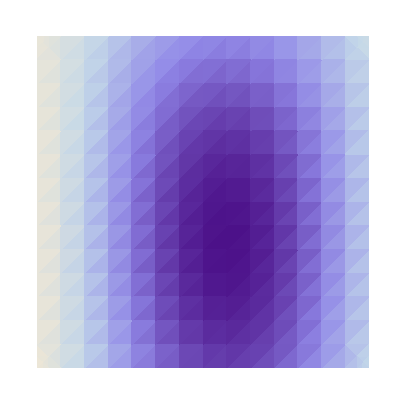

```mathematica
DensityPlot[Sin[x] Sin[y],{x,3,6},{y,1,2.5},Frame->False]
```

Here dark area means wind with higher horizontal speed.

A crest of wave

## About Automated Messy Wave

The line shows the crest of the wave. A trough means the wave peak at this place is a bit lower.

The speed difference of wind in the lower area and wind in normal area

```mathematica
u2[u1_,H_,h_]:=u1*(H/(1/2*h+H))
```

We used some approximations here, that the area lost compared to normal place is half the area of d*h, i.e., 1/2d*h.

Bernoulli equation gives the pressure difference,

```mathematica
p[ρ_,u_]:=1/2 ρ u
```

Pressure difference between the trough at in the first figure and normal place

```mathematica
dp[ρ_,u1_,H_,h_]=Simplify[p[ρ,u1]-p[ρ,u2[u1,H,h]]]
```

(h u1 ρ)/(2 h+4 H)

Now assume the wind is travelling at 20km/h, that is, in unit of m/s, h=0.002m, H=0.01m,  for atomosphere ρ=1.3kg/m^3

```mathematica
dp[1.3,5,0.01,0.002]
```

0.295455

This is really small. How about surface tension of water?
surface tensor coefficient of water is σ=72.75*10^-3N/m, we will use 7*10^-2N/m for simple.

```mathematica
σw=7*10^-2;
```

Radius of the the circle in figure 1

```mathematica
solR=R/.Solve[(R-0.002)^2+0.005^2==R^2,R][[1]]
```

0.00725

pressure difference caused by tension

```mathematica
dpst=σw/solR
```

9.65517

Intuitively,

```mathematica
dp[1.3,5,0.01,0.002]/dpst
```

0.0306006

Not too small.

## Wave Damping

Surface gravity wave damp expontentially.

```mathematica
RandomReal[-10,10]
```

{-9.6251,-3.44516,-4.29336,-7.72373,-8.3839,-4.15949,-2.6949,-7.18759,-7.07173,-3.5548}

```mathematica
Plot3D[Exp[-Abs[√(x^2+y^2)]-1],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
wave[L_,xn_,yn_]=Exp[-L √((x-xn)^2+(y-yn)^2)]
```

ⅇ^(-L √((x-xn)^2+(y-yn)^2))

```mathematica
twave[L_,x_,y_]=Total[Total[Table[wave[L,xn,yn],{xn,-10,10,2},{yn,-10,10,2}]]]
```

ⅇ^(-L √((-10+x)^2+(-10+y)^2))+ⅇ^(-L √((-8+x)^2+(-10+y)^2))+ⅇ^(-L √((-6+x)^2+(-10+y)^2))+ⅇ^(-L √((-4+x)^2+(-10+y)^2))+ⅇ^(-L √((-2+x)^2+(-10+y)^2))+ⅇ^(-L √(x^2+(-10+y)^2))+ⅇ^(-L √((2+x)^2+(-10+y)^2))+ⅇ^(-L √((4+x)^2+(-10+y)^2))+ⅇ^(-L √((6+x)^2+(-10+y)^2))+ⅇ^(-L √((8+x)^2+(-10+y)^2))+ⅇ^(-L √((10+x)^2+(-10+y)^2))+ⅇ^(-L √((-10+x)^2+(-8+y)^2))+ⅇ^(-L √((-8+x)^2+(-8+y)^2))+ⅇ^(-L √((-6+x)^2+(-8+y)^2))+ⅇ^(-L √((-4+x)^2+(-8+y)^2))+ⅇ^(-L √((-2+x)^2+(-8+y)^2))+ⅇ^(-L √(x^2+(-8+y)^2))+ⅇ^(-L √((2+x)^2+(-8+y)^2))+ⅇ^(-L √((4+x)^2+(-8+y)^2))+ⅇ^(-L √((6+x)^2+(-8+y)^2))+ⅇ^(-L √((8+x)^2+(-8+y)^2))+ⅇ^(-L √((10+x)^2+(-8+y)^2))+ⅇ^(-L √((-10+x)^2+(-6+y)^2))+ⅇ^(-L √((-8+x)^2+(-6+y)^2))+ⅇ^(-L √((-6+x)^2+(-6+y)^2))+ⅇ^(-L √((-4+x)^2+(-6+y)^2))+ⅇ^(-L √((-2+x)^2+(-6+y)^2))+ⅇ^(-L √(x^2+(-6+y)^2))+ⅇ^(-L √((2+x)^2+(-6+y)^2))+ⅇ^(-L √((4+x)^2+(-6+y)^2))+ⅇ^(-L √((6+x)^2+(-6+y)^2))+ⅇ^(-L √((8+x)^2+(-6+y)^2))+ⅇ^(-L √((10+x)^2+(-6+y)^2))+ⅇ^(-L √((-10+x)^2+(-4+y)^2))+ⅇ^(-L √((-8+x)^2+(-4+y)^2))+ⅇ^(-L √((-6+x)^2+(-4+y)^2))+ⅇ^(-L √((-4+x)^2+(-4+y)^2))+ⅇ^(-L √((-2+x)^2+(-4+y)^2))+ⅇ^(-L √(x^2+(-4+y)^2))+ⅇ^(-L √((2+x)^2+(-4+y)^2))+ⅇ^(-L √((4+x)^2+(-4+y)^2))+ⅇ^(-L √((6+x)^2+(-4+y)^2))+ⅇ^(-L √((8+x)^2+(-4+y)^2))+ⅇ^(-L √((10+x)^2+(-4+y)^2))+ⅇ^(-L √((-10+x)^2+(-2+y)^2))+ⅇ^(-L √((-8+x)^2+(-2+y)^2))+ⅇ^(-L √((-6+x)^2+(-2+y)^2))+ⅇ^(-L √((-4+x)^2+(-2+y)^2))+ⅇ^(-L √((-2+x)^2+(-2+y)^2))+ⅇ^(-L √(x^2+(-2+y)^2))+ⅇ^(-L √((2+x)^2+(-2+y)^2))+ⅇ^(-L √((4+x)^2+(-2+y)^2))+ⅇ^(-L √((6+x)^2+(-2+y)^2))+ⅇ^(-L √((8+x)^2+(-2+y)^2))+ⅇ^(-L √((10+x)^2+(-2+y)^2))+ⅇ^(-L √((-10+x)^2+y^2))+ⅇ^(-L √((-8+x)^2+y^2))+ⅇ^(-L √((-6+x)^2+y^2))+ⅇ^(-L √((-4+x)^2+y^2))+ⅇ^(-L √((-2+x)^2+y^2))+ⅇ^(-L √(x^2+y^2))+ⅇ^(-L √((2+x)^2+y^2))+ⅇ^(-L √((4+x)^2+y^2))+ⅇ^(-L √((6+x)^2+y^2))+ⅇ^(-L √((8+x)^2+y^2))+ⅇ^(-L √((10+x)^2+y^2))+ⅇ^(-L √((-10+x)^2+(2+y)^2))+ⅇ^(-L √((-8+x)^2+(2+y)^2))+ⅇ^(-L √((-6+x)^2+(2+y)^2))+ⅇ^(-L √((-4+x)^2+(2+y)^2))+ⅇ^(-L √((-2+x)^2+(2+y)^2))+ⅇ^(-L √(x^2+(2+y)^2))+ⅇ^(-L √((2+x)^2+(2+y)^2))+ⅇ^(-L √((4+x)^2+(2+y)^2))+ⅇ^(-L √((6+x)^2+(2+y)^2))+ⅇ^(-L √((8+x)^2+(2+y)^2))+ⅇ^(-L √((10+x)^2+(2+y)^2))+ⅇ^(-L √((-10+x)^2+(4+y)^2))+ⅇ^(-L √((-8+x)^2+(4+y)^2))+ⅇ^(-L √((-6+x)^2+(4+y)^2))+ⅇ^(-L √((-4+x)^2+(4+y)^2))+ⅇ^(-L √((-2+x)^2+(4+y)^2))+ⅇ^(-L √(x^2+(4+y)^2))+ⅇ^(-L √((2+x)^2+(4+y)^2))+ⅇ^(-L √((4+x)^2+(4+y)^2))+ⅇ^(-L √((6+x)^2+(4+y)^2))+ⅇ^(-L √((8+x)^2+(4+y)^2))+ⅇ^(-L √((10+x)^2+(4+y)^2))+ⅇ^(-L √((-10+x)^2+(6+y)^2))+ⅇ^(-L √((-8+x)^2+(6+y)^2))+ⅇ^(-L √((-6+x)^2+(6+y)^2))+ⅇ^(-L √((-4+x)^2+(6+y)^2))+ⅇ^(-L √((-2+x)^2+(6+y)^2))+ⅇ^(-L √(x^2+(6+y)^2))+ⅇ^(-L √((2+x)^2+(6+y)^2))+ⅇ^(-L √((4+x)^2+(6+y)^2))+ⅇ^(-L √((6+x)^2+(6+y)^2))+ⅇ^(-L √((8+x)^2+(6+y)^2))+ⅇ^(-L √((10+x)^2+(6+y)^2))+ⅇ^(-L √((-10+x)^2+(8+y)^2))+ⅇ^(-L √((-8+x)^2+(8+y)^2))+ⅇ^(-L √((-6+x)^2+(8+y)^2))+ⅇ^(-L √((-4+x)^2+(8+y)^2))+ⅇ^(-L √((-2+x)^2+(8+y)^2))+ⅇ^(-L √(x^2+(8+y)^2))+ⅇ^(-L √((2+x)^2+(8+y)^2))+ⅇ^(-L √((4+x)^2+(8+y)^2))+ⅇ^(-L √((6+x)^2+(8+y)^2))+ⅇ^(-L √((8+x)^2+(8+y)^2))+ⅇ^(-L √((10+x)^2+(8+y)^2))+ⅇ^(-L √((-10+x)^2+(10+y)^2))+ⅇ^(-L √((-8+x)^2+(10+y)^2))+ⅇ^(-L √((-6+x)^2+(10+y)^2))+ⅇ^(-L √((-4+x)^2+(10+y)^2))+ⅇ^(-L √((-2+x)^2+(10+y)^2))+ⅇ^(-L √(x^2+(10+y)^2))+ⅇ^(-L √((2+x)^2+(10+y)^2))+ⅇ^(-L √((4+x)^2+(10+y)^2))+ⅇ^(-L √((6+x)^2+(10+y)^2))+ⅇ^(-L √((8+x)^2+(10+y)^2))+ⅇ^(-L √((10+x)^2+(10+y)^2))

```mathematica
Plot3D[twave[10,x,y],{x,-20,20},{y,-20,20},PlotRange->{{-20,20},{-20,20},{0,0.2}}]
```

-Graphics3D-